# MS-C1650 - Numerical Analysis Week 19: Lecture 6: Randomized Quadratures

## Harri Hakula, 2021

## Monte Carlo

Notice: Load the MCDemo package first. Filename MCDemo.wl.

Our task is to estimate the value of π using the Monte Carlo method. Let us insert a circle with R=1/4 (area A_C=π (1/4)^2) in the centre of a rectangle with area A_R=4.
Next we sample points inside the rectangle (uniformly) and count the number of points that actually hit the circle. The ratio of the hits should be the ratio of the areas.

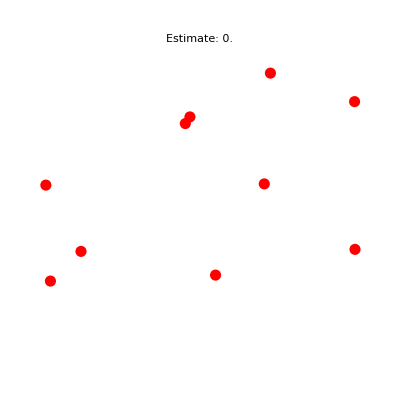

```mathematica
OneVisualRun[10]
```

## Convergence

The predicted rate of convergence is related to the number of sample points.

```mathematica
ms=Range[100,4000,100];
```

```mathematica
data=Monitor[Table[OneRun[m],{m,ms}],m];
```

```mathematica
err=Abs[Pi-data];
```

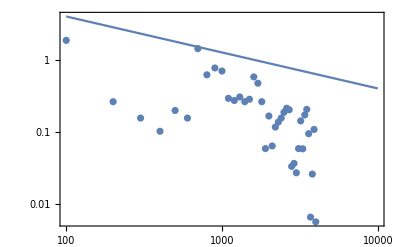

```mathematica
Show[ListLogLogPlot[Transpose[{ms,err}]],LogLogPlot[40x^(-1/2),{x,100,10000}],PlotRange->All,Frame->True,ImageSize->Large]
```

## QMC: Halton

QMC – Quasi Monte Carlo The idea is to cover the domain with somehow equispaced set of points. Here is an example of the so-called Halton points. A classical and nowadays outdated method.

```mathematica
vanderCorput[b_,n_]:=FromDigits[IntegerDigits[n,b],1/b]/b
```

```mathematica
Halton[n_]:={vanderCorput[2,n],vanderCorput[3,n]}
```

```mathematica
hpts=Table[Halton[k],{k,1,274}];
```

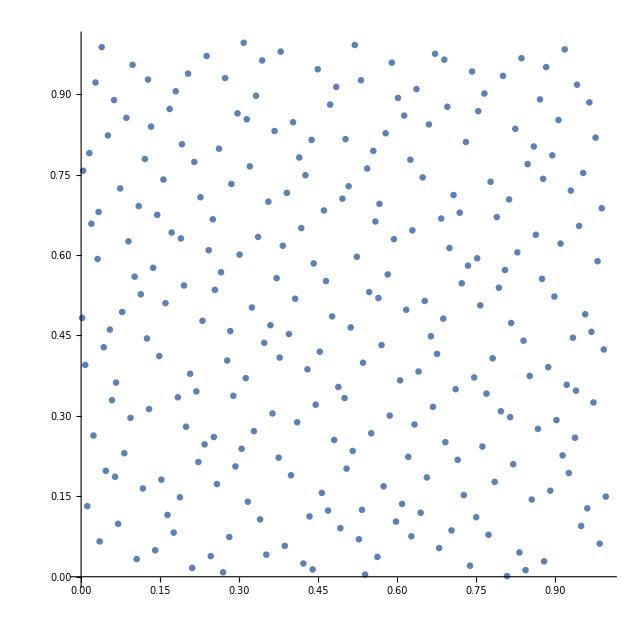

```mathematica
ListPlot[hpts,GridLines->{Subdivide[0,1,8],Subdivide[0,1,8]},AspectRatio->1,ImageSize->Large]
```

## QMC: 5D Example

Why bother? Well, if the problem is smooth enough, one can gain in the convergence rate!

```mathematica
exact=Integrate[Exp[-2z]Sin[x]y^3 Cos[u]Piecewise[{{v^5,v<1/2},{-1,1/2≤v<=1}}],{x,0,1},{y,0,1},{z,0,1},{u,0,1},{v,0,1}]
```

-(191 (-1+ⅇ^2) Sin[1/2]^2 Sin[1])/(1536 ⅇ^2)

```mathematica
vanderCorput[b_,n_]:=FromDigits[IntegerDigits[n,b],1/b]/b
```

```mathematica
Halton[n_]:={vanderCorput[2,n],vanderCorput[3,n],vanderCorput[5,n],vanderCorput[7,n],vanderCorput[11,n]}
```

```mathematica
fun[x_,y_,z_,u_,v_]:=Exp[-2z]Sin[x]y^3 Cos[u]Piecewise[{{v^5,v<1/2},{-1,1/2≤v<=1}}]
```

```mathematica
n=1000
```

1000

```mathematica
vals=Table[Apply[fun,Halton[k]],{k,1,n}];
```

```mathematica
acc=Accumulate@N@vals;
```

```mathematica
Length@acc
```

1000

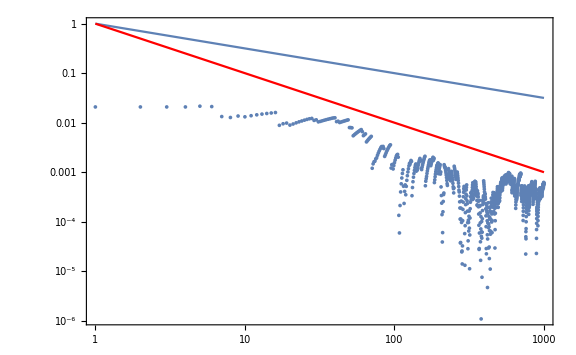

```mathematica
Show[LogLogPlot[x^(-1/2),{x,1,n},Axes->False],LogLogPlot[x^(-1),{x,1,n},Axes->False,PlotStyle->Red],ListLogLogPlot[Abs[exact-acc/Range[n]]],PlotRange->All,Frame->True,ImageSize->Large]
```